```mathematica
mu = 1.9
```

1.9

```mathematica
T0 = 273.15
```

273.15

```mathematica
Corr[T_,Ta_, mu_] := (T-Ta)/T^(mu-1)(2-mu)/(T^(2-mu) - Ta^(2-mu))
```

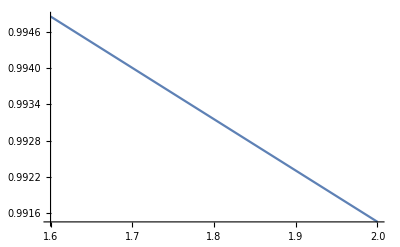

```mathematica
Plot[ Corr[ T0+20.0, T0+15, x], {x,1.6,2.0}]
```

```mathematica
Corr[T0+20.0,T0+15,1.9]
```

0.992301

```mathematica
NumberForm[%,10]
```

0.9923005413

```mathematica
Series [(T-Ta)/T^(alpha-1)(2-alpha)/(T^(2-alpha) - Ta^(2-alpha)), {Ta,T,3}]
```

1+((-1+alpha) (Ta-T))/(2 T)+((3-4 alpha+alpha^2) (Ta-T)^2)/(12 T^2)+((-3+4 alpha-alpha^2) (Ta-T)^3)/(24 T^3)+O[Ta-T]^4

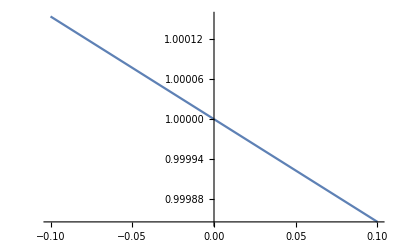

```mathematica
Plot[ Corr[T0+20.0, T0+20.0-x, 1.9], {x,-0.1,0.1}]
```